```mathematica
(* Dawid Bitner *)
(* przypadek prosty *)
(* parametry wejściowe - wysokość, prędkość zerowa *)
prosty[h_,v0_]:=Module[{g=9.81},
(* równanie różniczkowe *)
sol=DSolve[{y[0]==0,y'[0]==v0, y''[t]==g},y[t],t];
y[t_]=y[t]/. sol⟦1⟧;
sol2=Solve[h==y[t],t];
z[t_]:=h-y[t];
T=t/.Last[sol2];
Return[{T,Plot[z[t],{t,0,T},PlotStyle->Red,AxesLabel->{"czas","wysokość"},PlotLabel->"Wykres zależności położenia ciała od czasu"]}];

]
```

```mathematica
(* przypadek rzeczywisty *)
Clear[y,z];
(* parametry wejściowe - wysokość, prędkość zerowa, masa, wsp. oporu powietrza *)
rzeczywisty[h_,v0_,m_,k_]:=Module[{g=9.81},
(* równanie różniczkowe *)
sol=DSolve[{y[0]==0,y'[0]==v0, y''[t]+k/m*y'[t]==g},y[t],t];
y[t_]=y[t]/. sol⟦1⟧;
Quiet[sol2=Solve[h==y[t],t]];
z[t_]:=h-y[t];
T=t/.Last[sol2];
Return[{T,Plot[z[t],{t,0,T},PlotStyle->Red,AxesLabel->{"czas","wysokość"},PlotLabel->"Wykres zależności położenia ciała od czasu"]}];
]
```

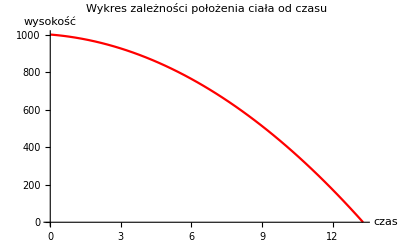

Ciało spadnie na ziemię po: 13.2954s.

```mathematica
solution=prosty[1000,10];
Show[solution⟦2⟧]
Print["Ciało spadnie na ziemię po: ",solution⟦1⟧, "s."];
```

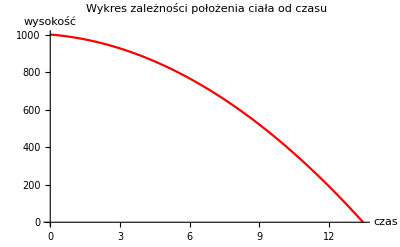

Ciało spadnie na ziemię po: 13.4657s.

```mathematica
solution=rzeczywisty[1000,10,100,0.5];
Show[solution⟦2⟧]
Print["Ciało spadnie na ziemię po: ",solution⟦1⟧, "s."];
```